# Упражнение 2 Дефиниране на функции и променливи. Грешки от закръгляване. Интерполационна формула на Лагранж.

## Дефиниране на променливи

```mathematica
a=10; (*Ако сложим точка и запетая накрая на реда, това потиска изхода.*)
b=x^2-12;
c=Simplify[a+b];
c(*Можем да видим стойността на дадена променлива, като просто напишем името й.*)
Clear[b];(*Изтрива стойността на b от паметта*)
b (*След като сме изтрили b  от паметта, за Mathematica това е просто параметър*)
```

-2+x^2

b

## Дефиниране на функции

```mathematica
f[x_]:=x^3-2x
g[x_,y_,z_]:=x+y+z
```

```mathematica
f[3]
f[x]
g[1,2,3]
```

21

-2 x+x^3

6

5/2

## Грешки от закръгляване

### Зад. Постройте графиките на функциите (x-2)^9 и -512+2304 x-4608 x^2+5376 x^3-4032 x^4+2016 x^5-672 x^6+144 x^7-18 x^8+x^9 в интервала [1.9, 2.1]

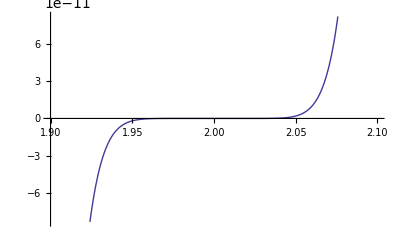

```mathematica
f[x_]:=(x-2)^9
Plot[f[x],{x,1.9,2.1}]
```

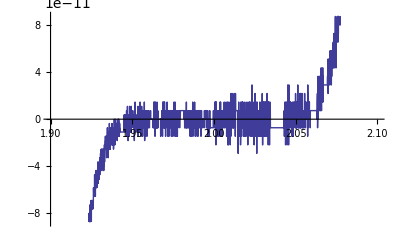

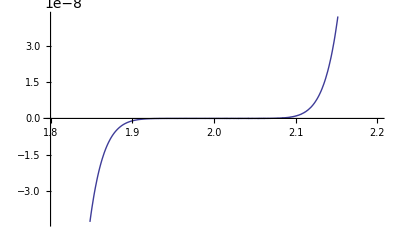

```mathematica
p[x_]:=-512+2304 x-4608 x^2+5376 x^3-4032 x^4+2016 x^5-672 x^6+144 x^7-18 x^8+x^9
Plot[p[x],{x,1.9,2.1}]
```

## Интерполационна формула на Лагранж

### Зад. Като се използва интерполационната формула на Лагранж, да се намери полином от пета степен, удовлетворяващ условията P(1)=2, P(2)=9,P(4)=41, P(6)=97.

```mathematica
l0[x_]:=((x-2)(x-4)(x-6))/((1-2)(1-4)(1-6))
l1[x_]:=((x-1)(x-4)(x-6))/((2-1)(2-4)(2-6))
l2[x_]:=((x-1)(x-2)(x-6))/((4-1)(4-2)(4-6))
l3[x_]:=((x-1)(x-2)(x-4))/((6-1)(6-2)(6-4))
p[x_]=Expand[2l0[x]+9l1[x]+41l2[x]+97l3[x]]
```

1-2 x+3 x^2

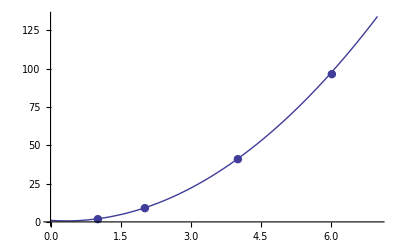

```mathematica
plot1=Plot[p[x],{x,0,7}];
plot2=ListPlot[{{1,2},{2,9},{4,41},{6,97}},PlotMarkers->●];
Show[plot1,plot2]
```